```mathematica
Clear["Global`*"]
```

```mathematica
LaunchKernels[48];
```

### Model

```mathematica
scaling=1;

a=scaling N[14.2/10]; a0=2 √3 a;
a1=a0{1/2 √3,-1/2};  a2=a0{1/2 √3,1/2};
δ1=a{-1/2,(√3)/2};δ2=a{-1/2,(-√3)/2};δ3=a{1,0};

(* == CsGraphene Parameters  == *)
t0=-2.7 / scaling; 
μVHSs={0.431523,0.839523,0.889523,1.413857,1.733857}/scaling;
Hk=With[{δ1=a{-1/2,(√3)/2},δ2=a{-1/2,(-√3)/2},δ3=a{1,0},
ϵc =0.5 t0,(* 0.44 t0,*)
ϵcp =0.52 t0 ,(* 0.46 t0,*)
ϵcs =-0.4 t0 , (*-0.44 t0,*)
t = 1.1 t0,
tp =1.1 t0 ,
t2 = 0.015 t0,
t3 = 0.1 t0 ,
th =0.025 t0,
tcs = 0.12t0
},
Compile[{{k,_Real,1}},
Module[{kx,ky,f1,f2,f3,c12,c23,c31,h1,h2,h3,hcs,sol},
{kx,ky}=k;
f1=Exp[ⅈ δ1.k];
f2=Exp[ⅈ δ2.k];
f3=Exp[ⅈ δ3.k];
c12=2Cos[(δ1-δ2).k];
c23=2Cos[(δ2-δ3).k];
c31=2Cos[(δ3-δ1).k];
h3=t3 (Exp[ⅈ k.(δ1-δ2-δ3)]+Exp[ⅈ k.(-δ1+δ2-δ3)]+Exp[ⅈ k.(-δ1-δ2+δ3)]);
hcs=ϵcs+2tcs(Cos[2 (δ1-δ3).k]+Cos[2(δ2-δ3).k]+Cos[2(δ1-δ2).k]);
sol=
{
{ϵc,t f3,t2 c23,t2 c31,t f2,t f1, t2 c12,h3*,0},
{t f3*,ϵcp,tp f2*,tp f1*,t2 c23, t2 c31, h3, t2 c12, th f3},
{t2 c23,tp f2, ϵcp, t2 c12, tp f3, h3*, t2 c31, t f1, th f1*},
{t2 c31, tp f1, t2 c12, ϵcp, h3*, tp f3, t2 c23, t f2, th f2*},
{t f2*,t2 c23, tp f3*,h3,ϵcp,t2 c12, tp f1*, t2 c31, th f2},
{t f1*, t2 c31, h3,tp f3*, t2 c12, ϵcp, tp f2*, t2 c23, th f1},
{t2 c12,h3*,t2 c31, t2 c23, tp f1, tp f2, ϵcp,t f3,th f3*},
{h3, t2 c12, t f1*,t f2*, t2 c31, t2 c23, t f3*, ϵc,0},
{0, th f3*, th f1,th f2, th f2*, th f1*,th f3, 0, hcs}
};
sol],RuntimeAttributes->{Listable}, CompilationTarget->"C",RuntimeOptions->"Speed"]];
(*Numerical derivative (with respect to kx) of Hk as defined above:*)
vx=With[{},
Compile[{{k,_Real,1}},
Module[{kx,ky,sol},
{kx,ky}=k;
sol={{0,(0.-4.2174000000000005 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),0.17253 Sin[2.13 kx+1.2297560733739028 ky],0.17253 Sin[2.13 kx-1.2297560733739028 ky],(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),0,-0.27 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),0},{(0.+4.2174000000000005 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],0,(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],0.17253 Sin[2.13 kx+1.2297560733739028 ky],0.17253 Sin[2.13 kx-1.2297560733739028 ky],-0.27 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),0,(0.-0.09585 ⅈ) ⅇ^(ⅈ (0.+1.42 kx))},{0.17253 Sin[2.13 kx+1.2297560733739028 ky],(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),0,0,(0.-4.2174000000000005 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),-0.27 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),0.17253 Sin[2.13 kx-1.2297560733739028 ky],(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),(0.-0.047925 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx]},{0.17253 Sin[2.13 kx-1.2297560733739028 ky],(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),0,0,-0.27 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),(0.-4.2174000000000005 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),0.17253 Sin[2.13 kx+1.2297560733739028 ky],(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),(0.-0.047925 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx]},{(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],0.17253 Sin[2.13 kx+1.2297560733739028 ky],(0.+4.2174000000000005 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],-0.27 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),0,0,(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],0.17253 Sin[2.13 kx-1.2297560733739028 ky],(0.+0.047925 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky))},{(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],0.17253 Sin[2.13 kx-1.2297560733739028 ky],-0.27 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),(0.+4.2174000000000005 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],0,0,(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],0.17253 Sin[2.13 kx+1.2297560733739028 ky],(0.+0.047925 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky))},{0,-0.27 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),0.17253 Sin[2.13 kx-1.2297560733739028 ky],0.17253 Sin[2.13 kx+1.2297560733739028 ky],(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),(0.+2.1087000000000002 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),0,(0.-4.2174000000000005 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),(0.+0.09585 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx]},{-0.27 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),0,(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-2.1087000000000002 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],0.17253 Sin[2.13 kx-1.2297560733739028 ky],0.17253 Sin[2.13 kx+1.2297560733739028 ky],(0.+4.2174000000000005 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],0,0},{0,(0.+0.09585 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],(0.+0.047925 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),(0.+0.047925 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),(0.-0.047925 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-0.047925 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-0.09585 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),0,-0.648 (4.26 Sin[2 (-2.13 kx-1.2297560733739028 ky)]+4.26 Sin[2 (-2.13 kx+1.2297560733739028 ky)])}};
sol],RuntimeAttributes->{Listable}, CompilationTarget->"C",RuntimeOptions->"Speed"]];

Nb=Length[Hk[{0,0}]]; (*Number of bands*)
e=ConstantArray[1,{1,Nb}]; ev=ConstantArray[{1},{1,Nb}]; (*Tensors used in calculation of the polarizability*)
(*Functions used in the calculation of the polarizability: *)
ΔfΔϵ=Compile[{{ϵ,_Real,1}},
Module[{ϵk,ϵkq,sol},
{ϵk,ϵkq}=ϵ;
If[Abs[ϵk-ϵkq]>=10^-7, (*Check CUTOFF WAS CHANGED FROM 10^-7*)
sol=(1/(Exp[ϵk]+1)-1/(Exp[ϵkq]+1))1/(ϵk-ϵkq),
sol= 1/(-2(1+Cosh[ϵk]))
];
sol],
RuntimeAttributes->{Listable},CompilationTarget->"C",RuntimeOptions->"Speed"];

CTto1BZ[q_]:=Block[{iq,jq},
{iq,jq}=q;
{iq,jq}=If[iq+jq>1,{iq-1,jq-1},{iq,jq}];
(*MyFloor[x_]:=-Floor[-x+0.5]*)
(*{iq,jq}={iq,jq}-{MyFloor[-0.5 jq+iq],MyFloor[-0.5 iq+jq]};*)
{iq,jq}={iq,jq}-(-Floor[-#+0.5])&[{-0.5 jq+iq,-0.5 iq+jq}];
{iq,jq}];

kBoltz = 0.00008617;

(* == Direct Lattice == *)
kgr={0,0};  kpr=1/3*(2 a1-a2);  kmr=1/2(a1+a2);  kkr=1/3(a1-2 a2);
Ac=1.(*a0^2 Sin[VectorAngle[a1,a2]]*);

(* == Reciprocal Lattice Vectors == *)
{b1,b2}=2 π Inverse[Transpose[{a1,a2}]]; b3=-( b1+b2);  kg={0,0};  kp=1/3*(2 b1+b2);    km=1/2(b1+b2);  kk=1/3(b1+2 b2);hxg[color_,vv_,kk_,kp_]:={Thickness[vv],color,Line[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}]};
BZhex=hxg[Black,0.02,kk,kp];
BZArea=Polygon[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}];

IndicesCTchunk[n_,nchunks_,ichunk_]:=Table[1/n{i,j},{i,0,n-1},{j,(ichunk-1)Floor[n/nchunks],(ichunk-1)Floor[n/nchunks]+Floor[(n-1)/nchunks]}];  

IdxCTqMΓM[n_,nsteps_]:=ParallelTable[1/n{i,i},{i,-Floor[(n-1)/2]-1,Ceiling[(n-1)/2],Floor[n/nsteps]}];  
IdxCTqMΓMB[n_,nsteps_]:=ParallelTable[1/n{i,0},{i,-Floor[(n-1)/2]-1,Ceiling[(n-1)/2],Floor[n/nsteps]}];  
IdxCTqMΓMC[n_,nsteps_]:=ParallelTable[1/n{0,i},{i,-Floor[(n-1)/2]-1,Ceiling[(n-1)/2],Floor[n/nsteps]}]; 
IdxCTqKΓKp[n_,nsteps_]:=ParallelTable[1/n{i,2i},{i,-Floor[n/3],Ceiling[(n-1)/3],Floor[n/nsteps]}];  
IdxCTqKΓKpB[n_,nsteps_]:=ParallelTable[1/n{i,-i},{i,-Floor[n/3],Ceiling[(n-1)/3],Floor[n/nsteps]}];  
IdxCTqKΓKpC[n_,nsteps_]:=ParallelTable[1/n{-2i,-i},{i,-Floor[n/3],Ceiling[(n-1)/3],Floor[n/nsteps]}]; 
IdxCTqMΓMExtended[n_,nsteps_]:=ParallelTable[1/n{i,i},{i,0,2(n-1),Floor[n/nsteps]}];  
IdxCTqMΓMBExtended[n_,nsteps_]:=ParallelTable[1/n{i,0},{i,0,2(n-1),Floor[n/nsteps]}];  
IdxCTqKΓKpExtended[n_,nsteps_]:=ParallelTable[1/n{i,2i},{i,-3Floor[n/3],3Ceiling[(n-1)/3],Floor[n/nsteps]}];  
IndicesrutaKΓMK[n_]:=Module[{ruta1,ruta2,ruta3,ruta4,ruta5,ruta6},
ruta1=Table[1/n{i,2i},{i,Ceiling[(n-1)/3],1,-1}];k1=Length[ruta1];
ruta2=Table[1/n{i,i},{i,0,Ceiling[(n-1)/2]-1,2}];  k2=k1+Length[ruta2];
ruta3=Table[1/2{1,1} + (1/3{i,2i}-1/2{i,i})1/n,{i,0,n,6}]; k3=k2+Length[ruta3];
Join [ruta1,ruta2,ruta3]
];
Ac
```

Compile::nogen: A library could not be generated from the compiled function.

1.

### Bands

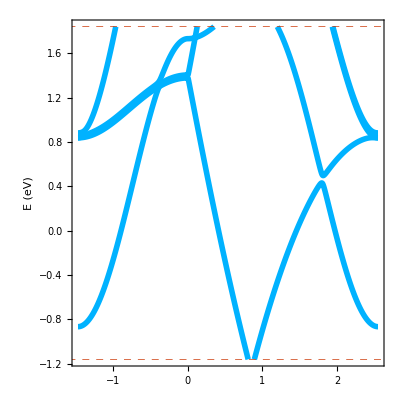

0.251523

μChub

867

```mathematica
rutaΓMKΓ[n_]:=Module[{ruta1,ruta2,ruta3,ruta4,ruta5,ruta6},
(*This functions creates a path in k space where bands will be calculated*)
ruta1=Table[km i/n,{i,0,n,2/√3}]; k1=Length[ruta1];
ruta2=Table[km + (kk-km)i/n,{i,1,n,2}];  k2=k1+Length[ruta2];
ruta3=Table[kk(n-i)/n,{i,1,n}]; k3=k2+Length[ruta3];
Join [ruta1,ruta2,ruta3]];  
rutaKΓMK[n_]:=Module[{ruta1,ruta2,ruta3,ruta4,ruta5,ruta6},
ruta1=Table[kk(n-i)/n,{i,1,n}];k1=Length[ruta1];
ruta2=Table[km i/n,{i,0,n,2/√3}];  k2=k1+Length[ruta2];
ruta3=Table[km + (kk-km)i/n,{i,1,n,2}]; k3=k2+Length[ruta3];
Join [ruta1,ruta2,ruta3]
]; 

(*This function plots the bands: *)
μ0=μVHS-2.0;
μf=μVHS+1.0;
plt[rangea_,rangeb_,fun_,kpoints_]:=Show[ListPlot[fun,Joined->True,PlotRange->{rangea,rangeb},PlotStyle->{{Hue[0.55,1,1],Thickness[0.01]}}, Frame->True, FrameStyle->Directive[Black,Thick],
FrameTicks->{{Automatic,None},{(*qpathTicks*)Automatic,None}},AspectRatio->1,
GridLines->{{k1,k2,k3},{{μ0,Directive[Red,Thick, Dashed]},{μf,Directive[Red,Thick, Dashed]}}},
GridLinesStyle->Directive[Dashed], ImageSize->400,FrameTicksStyle->Directive[Black,20],
LabelStyle->Directive[Normal,20,Black,FontFamily->"CMU Serif"],PlotRangePadding->0, FrameLabel->{{"E (eV)",None},{None,None}},AxesOrigin->{0,-1000}]
];
(*Calculate bands along path in k space: *)
kpoints=1000;
rutaq = "ΓMKΓ";
If[rutaq=="ΓMKΓ",
rt=rutaΓMKΓ[kpoints];
qpathTicks={{1,"Γ"},{k1,"M"},{k2,"K"},{k3,"Γ"}},
If[rutaq=="KΓMK",
rt=rutaKΓMK[kpoints];
qpathTicks={{1,"K"},{k1,"Γ"},{k2,"M"},{k3,"K"}},
Print["Error in defining path!"]
];
];
Hrt=Hk[rt];
Ek=Map[Eigenvalues,Hrt];
Ek=Map[Sort,Ek];
Epath = ConstantArray[True,Nb];
kARPES=Table[(i-k1)1.474/k1,{i,Ek//Length}];

Do[
Epath[[j]]=Table[{kARPES[[i]],Ek[[i,j]](*-μVHSs[[1]]*)(*+.18-3.02*)},{i,Ek//Length}];,
{j,1,Nb}];

(*ϵa=-4/scaling; ϵb=5.5/scaling; *)
ϵa=μ0 ;ϵb=μf ;
nVHS=1;
plt[ϵa, ϵb,Epath,kpoints]
Epath3nn=Epath;
μVHSs[[nVHS]]-0.18
μChub
k1
```

### Mesh Chunks

```mathematica
(*Visualization of how the mesh is divided into chunks*)
hxg[color_,vv_,kk_,kp_]:={Thickness[vv],color,Line[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}]}
nkTest=6 2;nchunksTest=nkTest/3;
kij=Flatten[IndicesCTchunk[nkTest,1,1],1];
kb=kij.{b1,b2};
Manipulate[
PlotLat=Graphics[{
hxg[Red,0.01,kk,kp],
Translate[hxg[Red,0.01,kk,kp],b1],
Translate[hxg[Red,0.01,kk,kp],b2],
Translate[hxg[Red,0.01,kk,kp],b1+b2],
Translate[hxg[Red,0.01,kk,kp],-b1],
Translate[hxg[Red,0.01,kk,kp],-b2],
Translate[hxg[Red,0.01,kk,kp],-b1-b2],
kijch=Flatten[IndicesCTchunk[nkTest,nchunksTest,i],1];
kbch=kijch.{b1,b2};
PointSize[0.02],Red,Opacity[0.3],Point[Flatten[kb,0]],Thick,
PointSize[0.01],Black,Opacity[0.3],Point[Flatten[kbch,0]],Thick,
Red, Arrow[{{0,0},b1}],Blue, Arrow[{{0,0},b2}]
},ImageSize->300,Frame->True,PlotLabel->"Momentum-Space MP Lattice"]
,{i,1,nchunksTest,1}]
```

Table::iterb: Iterator {i,0,-1+nkTest} does not have appropriate bounds.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[kb,0].

### PBCs

```mathematica
(*Visualization of periodic boundary conditions*)
hxg[color_,vv_,kk_,kp_]:={Thickness[vv],color,Line[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}]}
(*nkTest must be odd, otherwise, k+q points do fall in the MP k lattice. Furthermore, nkTest must be an multiple of 3 to have points exactly at kk and kp*)
nkTest=6 2;nchunksTest=1;nqTest= nkTest;
kqFoldBack=True;
qFoldBack=True;
kij=Flatten[IndicesCTchunk[nkTest,nchunksTest,1],1];
If[False,kij=Map[Mod[#,1]&,kij]];
If[False,kij=Map[CTto1BZ,kij]];
kb=kij.{b1,b2};

qi=IndicesrutaKΓMK[nkTest];
If[qFoldBack,qi=Map[Mod[#,1]&,qi]];
If[True,qi=Map[CTto1BZ,qi]];
qb=qi.{b1,b2};
Manipulate[

PlotLat=Graphics[{hxg[Red,0.01,kk,kp],
(*kq=(kijᵀ+{1,1}/nkTest)ᵀ;
If[True,kq=Map[Mod[#,1]&,kq]];*)
kqb=kq.{b1,b2};
Thick,PointSize[0.03],Black,Opacity[0.3],Point[Flatten[kb,0]],
PointSize[0.05],Red,Opacity[0.3],Point[kb[[i]]],
kb1BZ=CTto1BZ[kij[[i]]].{b1,b2};
PointSize[0.05],Purple,Opacity[0.3],Point[kb1BZ],
(*If[kqFoldBack,kq=Map[Mod[#,1]&,kq]];*)
(*If[True,kq=Map[CTto1BZ,kq]];*)
(*kqb=kq.{b1,b2};*)
(*Thick,PointSize[0.03],Green,Opacity[1],Point[Flatten[kqb[[i]],0]],*)
Thick,Red,Opacity[1],Arrow[{{0,0},b1}],
Blue,Arrow[{{0,0},b2}],
Style[{Text["b1",b1 1.05],Text["b2",b2 1.05],Text["kk",kk 1.1],Text["kp",kp 1.1]},{Medium,Red}]
},ImageSize->300,Frame->True,PlotLabel->"Momentum-Space MP Lattice"],{i,1,kb//Length,1}]
a1.b1/(2π)
```

1.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[kb,0].

Part::partd: Part specification kb⟦144⟧ is longer than depth of object.

Part::partd: Part specification kij⟦144⟧ is longer than depth of object.

Set::shape: Lists {iq,jq} and kij⟦144⟧ are not the same shape.

Set::shape: Lists {iq,jq} and If[iq+jq>1,{iq-1,jq-1},{iq,jq}] are not the same shape.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of iq+Floor[0.5-iq+0.5 jq].

### Lattices

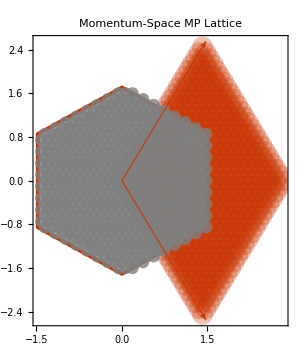
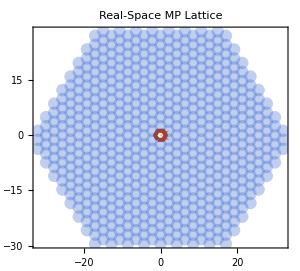

{1.47493,-2.55465}

```mathematica
hxg[color_,vv_,kk_,kp_]:={Thickness[vv],color,Line[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}]}

nkTest=6 4;nchunksTest=1;nqTest= nkTest;
kij=Flatten[IndicesCTchunk[nkTest,nchunksTest,1],1];
rij=nkTest Map[CTto1BZ,Flatten[IndicesCTchunk[nkTest,nchunksTest,1],1]];
kb=kij.{b1,b2};
rij =Delete[rij,Position[rij,{0,0}]];
(*rij=(rijᵀ-{1,1}(nkTest-1)/2)ᵀ;*)
(*rij=Map[CTto1BZ,rij];*)
R=rij.{+a1,-a2};

PlotLat=Row[{Graphics[{hxg[Red,0.01,kk,kp],
PointSize[0.05],Red,Opacity[0.3],Point[Flatten[kb,0]],
PointSize[0.03],Gray,Opacity[0.8],Point[Map[CTto1BZ,kij].{b1,b2}],
Thick,Red,Arrow[{{0,0},b1}],Arrow[{{0,0},b2}]},ImageSize->300,Frame->True,PlotLabel->"Momentum-Space MP Lattice"],
Graphics[{hxg[Red,0.01,kkr,kpr],
PointSize[0.03],Blue,Opacity[0.3],Point[Flatten[R,0]],
Thick,Red,Arrow[{{0,0},a1}],Arrow[{{0,0},a2}]},ImageSize->300,Frame->True,PlotRange->All,PlotLabel->"Real-Space MP Lattice"]
}]
b1
```

## Main Functions

### Susceptibility and Screened Interaction

Parameters: {s, ω0, n, δϵ} = {1,17.,1,0.03}

nk= 6

Points in k mesh: 36

μVHS = 4.077

```mathematica
n = 400; (*Sets the size of the k-mesh*)
μVHS=μVHSs[[2]];
nk=6n;  (*This forms gives always a nk odd and multiple of 3, desirable for mesh symmetry*)(*Number of k-points in mesh will be nk^2. Written in this form so it will always be an odd multiple of 3 (important for the symmetry of the mesh).*)
(*Create directory to save files*)

FilePath=FileNameJoin[{NotebookDirectory[],"Data_Cs"}];
If[!FileExistsQ[FilePath],
CreateDirectory[FilePath]]
(*Memory cuttofs for each device*)
LapMaxMemory = 8;
PCMaxMemory = 80;
MaxRAMallowed =LapMaxMemory;
Print["nk= ",nk]
Print["Points in k mesh: ",nk^2]
Print["μVHS = ",μVHS];

ωf=5;
 ω0=0.;
nω=1500;
η=0.01;
Πloop[μkbT_]:=(
 Δω=(ωf-ω0)/nω;
 ω=Table[ω0+(i-1) Δω,{i,1,nω}];
nch=nk/3;
solchunks=Table[Table[0,{ω//Length}],{μkbT//Length}];
Print["Diagonalizing and building tensors..."];
Do[
time0=AbsoluteTime[];
kb=Flatten[IndicesCTchunk[nk,nch,ichunk],1].{b1,b2};
Hkb=Hk[kb];
Eψk=Map[Eigensystem,Hkb];
vxk=vx[kb];
Ek=Eψk[[All,1]]; ψk=Eψk[[All,2]];

EkTensor=Flatten[KroneckerProduct[Ek,e]];
EkqTensor=Flatten[KroneckerProduct[e,Ek]];
ΔE=EkTensor-EkqTensor;
EkEkq={EkTensor,EkqTensorᵀ}ᵀ;
Fv=Flatten[Table[Norm[ψk[[i,n]]*ᵀ.vxk[[i]].ψk[[i,m]]]^2,{i,1,vxk//Length},{n,1,Nb},{m,1,Nb}],2];
Do[
μ=μkbT[[l,1]];
kbT=μkbT[[l,2]];
ΔETensor=(EkEkq-μ)/kbT;

Πk=ΔfΔϵ[ΔETensor]*Fv/kbT ;
solchunks[[l]]+=(2 Norm[b1]^2)/(4 π^2 nk^2)Map[Total[Πk/(ΔE+ⅈ η+#)]&,ω];
,{l,1,μkbT//Length}];
If[ichunk==1, Print["Estimated time: ",(AbsoluteTime[]-time0)*nch/60, " mins"]]
,{ichunk,1,nch}];
solchunks)
```

nk= 2400

Points in k mesh: 5760000

μVHS = 0.839523

```mathematica
Temp=1;
μ0=μVHS-2.0;
μf=μVHS+1.0;
δμ=0.1;
Print["Parameters: {n, Temp, η, ω0, ωf, nω} = ",{n, Temp, η,ω0,ωf,nω}]
ParamString=ToString[n]<>"_"<>ToString[Temp]<>"_"<>ToString[η]<>"_"<>ToString[ω0]<>"_"<>ToString[ωf]<>"_"<>ToString[nω];
DataPath=FileNameJoin[{FilePath,ParamString}];
If[!FileExistsQ[DataPath],
CreateDirectory[DataPath]];
FillingPath=FileNameJoin[{DataPath,"filling_"<>ToString[μ0]<>"_"<>ToString[μf]<>"_"<>ToString[δμ]}];
SigmaPath=FileNameJoin[{FillingPath,"σ.csv"}];
μlistkbT=Table[{i,kBoltz Temp },{i,μ0,μf,δμ}];
If[FileExistsQ[SigmaPath],
σ=ToExpression@Import[SigmaPath];
Print["Importing data. Done"];,
Print["No data found. Calculating..."];
Πω=Πloop[μlistkbT];
σ=Map[{ωᵀ,#}ᵀ&,Im[Πω]];
Export[SigmaPath,σ];
Print["Completed."];
];
```

Parameters: {n, Temp, η, ω0, ωf, nω} = {400,1,0.01,0.,5,1500}

Importing data. Done

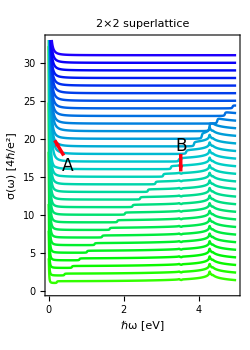
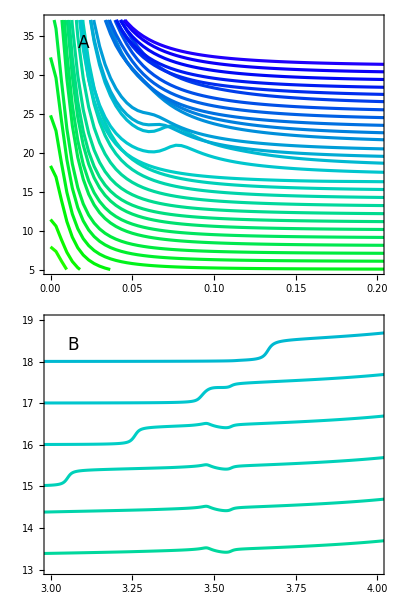

```mathematica
ColsMag[x_]:=Blend[{{0.,Hue[0.99]},{1,Hue[0.65]}},x];
ColsPy[x_]:=Blend[{{0,Hue[0.3]},{0.5,Hue[0.5,1,0.8]},{1,Hue[0.7]}},x];
ColsG[x_]:=Blend[{{0.,Hue[0.2,1,1]},{0.5,Hue[0.1]},{1,Hue[0.0]}},x];
Cols=ColsPy;
nμc=(μlistkbT//Length);
μColors= Table[{Cols[i/nμc],Thickness[0.007]},{i,0,nμc}];
μColorsi= Table[{Cols[i/nμc],Thickness[0.015]},{i,0,nμc}];
PlotSeq=Sequence[Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,15,FontFamily->"CMU Serif"],
LabelStyle->Directive[Normal,15,FontFamily->"CMU Serif"],AspectRatio-> 2 0.7,ImageSize->250];
ColLeg=BarLegend[{Cols,{0,1}},LegendLabel->"μ", LabelStyle->Directive[15,Black,FontFamily->"CMU Serif"],"Ticks"->{(*0,1*)},"TickLabels"->{(*"Away from vHS",*)" "},ImageSize->100];
ArrowSeq=Sequence[Hue[0.99],Arrowheads[0.05],Thickness[0.01]];
RecSeq=Sequence[EdgeForm[Gray],Opacity[0]];
TextSeq=Sequence[Black,17,FontFamily->"CMU Serif",Background->White];
LineSeq=Sequence[Gray,Dashed];
δσ=1;
PltR={{ω0,ωf},{0,33}};
PltRi1={{0,.2},{5,37}};
PltRi2={{3,4},{13,19}};
σCurves=Table[{σ[[i,All,1]]ᵀ,σ[[i,All,2]]+i δσ}ᵀ,{i,σ//Length}];
plot=ListPlot[σCurves,PlotStyle->μColors,PlotSeq,
PlotRange->PltR,
FrameLabel->{"ℏω [eV]","σ(ω) [4ℏ/e^2]"},PlotLabel->Style[(*"Cs-doped SLG"*)"2×2 superlattice",Black],Epilog->{
ArrowSeq,Arrow[{{3.52,18},{3.52,15.7}}],Arrow[{{0.4,17.8},{0.16,19.8}}],
(*RecSeq,Rectangle[PltRi1ᵀ[[1]],PltRi1ᵀ[[2]]],Rectangle[PltRi2ᵀ[[1]],PltRi2ᵀ[[2]]]*)
Text[Style["A",TextSeq],{0.5,16.4}],
Text[Style["B",TextSeq],{3.52,19}]
}];
inset1=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->150,AspectRatio->1,PlotSeq,PlotRange->PltRi1,Epilog->{Text[Style["A",TextSeq],{0.02,34}]}];
inset2=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->146,AspectRatio->1,PlotSeq,PlotRange->PltRi2,Epilog->{Text[Style["B",TextSeq],{3.07,18.4}]}];
plt=Row[{plot,Column[{inset1,inset2}](*,ColLeg*)}]
Export[FileNameJoin[{NotebookDirectory[],"Sigma_CsG.pdf"}],plt];
```

```mathematica
DFTLi=Import[FileNameJoin[{"/Users/saulherrera/Documents/Cálculos/Optical Signatures in Doped G Superlattices/","DFT_Li.txt"}],"Table"]
```

```mathematica
DFTLi//Dimensions
```

{2441}